# Simulation of Epidemic

E. M . de Morais, IFT-UNESP, Brazil

## Disease Propagation in a Box

### Defining Parameters

```mathematica
(* Clear all variables *)
Clear["Global`*"]

(* Set the notebook directory as the work directory *)
SetDirectory[NotebookDirectory[]];


(* NUMERICAL SIMULATION PARAMETERS *)

(* Constant velocity of individuals*)
Velocity = 0.1;

(* Population Size *)
Qtde=200;

(* Time element *)
δt=0.1;

(* Final time *)
FinalTime = 100.0;


(* PHYSICAL PARAMETERS *)

(* Infection distance radio *)
SphRad = 0.008;

(* Daily probability of cure of the symptomatic individual *)
ProbSymptomaticCure = 0.005;

(* Daily probability of death of the infected individual *)
ProbSymptomaticDeath = 0.0005;

(* Probability of infectious in case of contact *)
InfecProbByContact=1.0;

(* Limit days for the death of infected individual *)
DaysToSymptomaticDeath = 100;

(* Using colors to control the state of the individuals *)
Healthy = RGBColor[0,0.6,0.2];
Infected = Red;
Dead = RGBColor[0.0,0.,0.,0.];
Recovered = RGBColor[0.0,0.0,0.6];


ListPos = {Table[{RandomReal[{SphRad,1-SphRad}],RandomReal[{SphRad,1-SphRad}]},{Qtde}]};
ListVel0 = Table[Angle = RandomReal[{0,2π}];Velocity {Sin[Angle],Cos[Angle]},{Qtde}];
ListState= {Table[Healthy,{Qtde}]};

(*Inserting one infected *)
ListInfectedIndex = {1};
InfectionTiming= Table[0.0,{Qtde}];
ListState[[1,ListInfectedIndex[[-1]]]] = Infected;
InfectedCount = 1;
InfectedList = {};

(* NotInfected *)
ListNotInfectedIndex = Table[i,{i,2,Qtde}];
NotInfectedCount = Qtde-1;
NotInfectedList = {};

(* Deaths Counting *)
ListDeathsIndex = {};
DeathsCount = 0;
DeathsList = {};

(* Cures Counting *)
ListRecoveredIndex = {};
RecoveredCount = 0;
RecoveredList = {};
```

### Running the system

```mathematica
Monitor[Do[
NewPosList = {};
NewStateList = {};
(* Runnig trough particles *)
Do[
	(************************************************)
	(* Checking if position is outframing in x coordinate *)
	IndividualState = ListState[[-1,i]];
	RefIndividualPos = ListPos[[-1,i]];
	IndividualNewPos = ListPos[[-1,i]]+δt ListVel0[[i]];

	If[!(SphRad<IndividualNewPos[[1]]<1-SphRad),
		ListVel0[[i,1]] = -ListVel0[[i,1]];
		IndividualNewPos = ListPos[[-1,i]]+δt ListVel0[[i]];
	];
	
	(* Checking if position is outframing in y coordinate *)
	IndividualNewPos = ListPos[[-1,i]]+δt ListVel0[[i]];
	If[!(SphRad<IndividualNewPos[[2]]<1-SphRad),
		ListVel0[[i,2]] = -ListVel0[[i,2]];
		IndividualNewPos = ListPos[[-1,i]]+δt ListVel0[[i]];
		];
	
	(* Updating Position *)	
	AppendTo[NewPosList,IndividualNewPos];

	(************************************************)
	(* Checking state of particle *)
	
	If[(ListState[[-1,i]]===Infected)||(ListState[[-1,i]]===Recovered),

		(* In the case where the individual is sick or cured, do nothing *)
		IndividualState=ListState[[-1,i]];
	,
		
		(* Checking every pair *)
		Do[
			LoopIndividualState = ListState[[-1,j]];
			If[(LoopIndividualState===Infected),
				LoopIndividualPos = ListPos[[-1,j]];
				LoopDist = Norm[RefIndividualPos-LoopIndividualPos];
				
				(* Another infected *)
				If[(Random[]<InfecProbByContact)&&(LoopDist<2SphRad),
					IndividualState = Infected;
					
					If[(!MemberQ[Sort[ListInfectedIndex],i])&&(MemberQ[ListNotInfectedIndex,i]),
						ListNotInfectedIndex = DeleteCases[ListNotInfectedIndex,i];
						NotInfectedCount--;
						AppendTo[ListInfectedIndex,i];
						InfectedCount++;
					];
				];
			];
		,{j,1,Qtde}]

	];
	
	
	AppendTo[NewStateList,IndividualState];

,{i,1,Qtde}];

AppendTo[ListPos,NewPosList];
AppendTo[ListState,NewStateList];

	(************************************************)
	(* Incrementing sick count *)
	ListSickIndexCpy = ListInfectedIndex;
	Do[
		InfectionTiming[[index]] = InfectionTiming[[index]]+δt;
		
		(* Infected Patients *)
		ListState[[-1,index]] = Infected;
		
				
		(* Pacient Recoverd *)
		If[(Random[]<ProbSymptomaticCure)&&((!MemberQ[Sort[ListRecoveredIndex],index])(*&&(!MemberQ[Sort[ListRecoveredIndex],index])*)),
				ListInfectedIndex = DeleteCases[ListInfectedIndex,index];
				AppendTo[ListRecoveredIndex,index];
				InfectedCount--;
				RecoveredCount++;
				ListState[[-1,index]] = Recovered;
			];
			
			(* Pacient Died*)
			If[((Random[]<ProbSymptomaticDeath)&&((!MemberQ[Sort[ListRecoveredIndex],index])&&(!MemberQ[Sort[ListRecoveredIndex],index])))||((InfectionTiming[[index]]>DaysToSymptomaticDeath)),
				ListInfectedIndex = DeleteCases[ListInfectedIndex,index];
				AppendTo[ListDeathsIndex,index];
				InfectedCount--;
				DeathsCount++;
				ListState[[-1,index]] = Dead;
			];
		
						
	,{index,ListInfectedIndex}];

	AppendTo[InfectedList,{t,InfectedCount}];
	AppendTo[DeathsList,{t,DeathsCount}];
	AppendTo[RecoveredList,{t,RecoveredCount}];
	AppendTo[NotInfectedList,{t,NotInfectedCount}];
	
	
	
,{t,0,FinalTime,δt}],100.t/FinalTime]

FinalNotInfectedList=NotInfectedList[[1;;-1]];
FinalInfectedList=InfectedList[[1;;-1]];
FinalRecoveredList=RecoveredList[[1;;-1]];
FinalDeathsList=DeathsList[[1;;-1]];
```

### Results

```mathematica
anim=Manipulate[

GraphicsGrid[{

{
	ListPlot[{NotInfectedList[[1;;n]],InfectedList[[1;;n]],RecoveredList[[1;;n]],DeathsList[[1;;n]]},PlotStyle->{Healthy,Infected,Recovered,Black},
	Frame->True,ImagePadding->1,AspectRatio->0.4,ImageSize->{400,Automatic},PlotRange->{{0,FinalTime},{-0.1Qtde,1.1Qtde}},
	Frame->True,PlotRange->{{0,1},{0,1}},
	FrameTicksStyle->{RGBColor[0,0,0,0],RGBColor[0,0,0,0]},
	FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->0,ImageSize->{400,Automatic},
	PlotLegends->Placed[
		PointLegend[
			{
				Directive[Healthy,AbsolutePointSize[6]],
				Directive[Infected,AbsolutePointSize[6]],
				Directive[Recovered,AbsolutePointSize[6]],
				Directive[Black,AbsolutePointSize[6]]
			},
				{"Susceptible","Infected","Recovered","Dead"},
				LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->None,Background->RGBColor[1,1,1,0.8]]&),
				LegendLayout->"Column"]
			,{{0.82,0.97},{0.5,1}}]
		]
},{
	Graphics[
		Table[{ListState[[n,i]], Disk[ListPos[[n,i]],SphRad]},{i,1,Length[ListPos[[n]]]}],
		Frame->True,PlotRange->{{0,1},{0,1}},
		FrameTicksStyle->{RGBColor[0,0,0,0],RGBColor[0,0,0,0]},
		FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->1,ImageSize->{400,Automatic}
	] 
}
	
},Spacings->{0,-122}] 
,{n,1,2+0.99FinalTime/δt,1}]
```

### High Definition Video Export

```mathematica
FrameQtt=1+FinalTime/δt;
Step = 2;
FramesPerSecond = 25;


Monitor[GraphicsList = Table[


GraphicsGrid[{

{
ListPlot[{NotInfectedList[[1;;n]],InfectedList[[1;;n]],RecoveredList[[1;;n]],DeathsList[[1;;n]]},PlotStyle->{Healthy,Infected,Recovered,Black},
Frame->True,ImagePadding->1,AspectRatio->0.4,ImageSize->{400,Automatic},PlotRange->{{0,FinalTime},{-0.1Qtde,1.1Qtde}},
Frame->True,PlotRange->{{0,1},{0,1}},
FrameTicksStyle->{RGBColor[0,0,0,0],RGBColor[0,0,0,0]},
FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->0,ImageSize->{400,Automatic},
PlotLegends->Placed[PointLegend[{
Directive[Healthy,AbsolutePointSize[6]],
Directive[Infected,AbsolutePointSize[6]],
Directive[Recovered,AbsolutePointSize[6]],
Directive[Black,AbsolutePointSize[6]]},

{"Susceptible","Infected","Recovered","Dead"},
LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->None,Background->RGBColor[1,1,1,0.8]]&),LegendLayout->"Column"],{{0.82,0.97},{0.5,1}}]
]
},

{
Graphics[

(*{Red, Disk[#,SphRad]}&/@ListPos[[n]]*)
Table[{ListState[[n,i]], Disk[ListPos[[n,i]],SphRad]},{i,1,Length[ListPos[[n]]]}],

Frame->True,PlotRange->{{0,1},{0,1}},
FrameTicksStyle->{RGBColor[0,0,0,0],RGBColor[0,0,0,0]},
FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->1,ImageSize->{400,Automatic}
] 
}

},Spacings->{0,-122}] 



,{n,1,FrameQtt,Step}],Row[{"%: ",100.n/FrameQtt}]];

(*Export["Disease-Propagation-Simulation.avi",GraphicsList,FrameRate->FramesPerSecond]*)
Export["Disease-Propagation-Simulation.gif",GraphicsList,FrameRate->FramesPerSecond]
```

Disease-Propagation-Simulation.avi

Disease-Propagation-Simulation.gif

```mathematica
Export["Disease-Propagation-Simulation.gif",GraphicsList,FrameRate->FramesPerSecond]
```

Export::infer: Cannot infer format of file MyAutorun3.mp4.

$Failed

```mathematica
Export
```

## Compatibility of the simulation with the SIRD model

From the simulation results, it can be seen that the curves present the typical pattern of evolution of SIRD. The differential equations of this model describe the dynamics of four functions that account, respectively, for the number of individuals susceptible to contagion (S), infected (I), recovered (R) and killed (D)  (arXiv:2003.06031):

dS/dt=-β S I 
dI/dt=β S I -(γ+α)I
dR/dt=γ I 
dD/dt=α I

Note that the sum S_0 = S+I+R+D  is always constant and together with {α,β,γ}, composes the set of parameters of the model. The initial time is defined as the time when the first infection occurs.  In this way, I(0) = 1 , R(0) = 0 and D(0) = 0 .  Moreover, it is assumed for simplicity that only contagion causes fatalities.

```mathematica
FinalNotInfectedList=NotInfectedList[[1;;-1]];
FinalInfectedList=InfectedList[[1;;-1]];
FinalRecoveredList=RecoveredList[[1;;-1]];
FinalDeathsList=DeathsList[[1;;-1]];
```

```mathematica
fn[x_,OptionsPattern[]]:=k[x,OptionValue[opt2]]
```

```mathematica
ClearAll[SIRDModelSolve,SIRDModelChiSqrd]

(* Numerical solve of SIRD Model *)

Options[SIRDModelSolve] = {I0 -> 1};
SIRDModelSolve[tfim_,{S0_,α_,β_,γ_},OptionsPattern[]]:=Block[{},
NDSolveValue[{
s'[t]==-β s[t] i[t],s[0]==S0,
i'[t]==β s[t] i[t]-γ i[t]-α i[t],i[0]==OptionValue[I0],
r'[t]==γ i[t],r[0]==0,
d'[t]==α i[t],d[0]==0
},{s,i,r,d},{t,0,tfim}]
];

SIRDModelChiSqrd[tfim_,{S0_,α_,β_,γ_}]:=Block[{𝕤,𝕚,𝕣,𝕕,χ2},
{𝕤,𝕚,𝕣,𝕕} = SIRDModelSolve[tfim,{S0,α,β,γ}];
χ2=0;
χ2+=Total[(𝕤[#[[1]]]-#[[2]])^2&/@FinalNotInfectedList];
χ2+=Total[(𝕚[#[[1]]]-#[[2]])^2&/@FinalInfectedList];
χ2+=Total[(𝕣[#[[1]]]-#[[2]])^2&/@FinalRecoveredList];
χ2+=Total[(𝕕[#[[1]]]-#[[2]])^2&/@FinalDeathsList];
χ2
];
```

First of all, we have to find some rough estimate for parameters and its confidence interval. There is no methodology for this. Just testing. We`re gonna fix the parameter  S_0 since we do know the population size in the simulation.

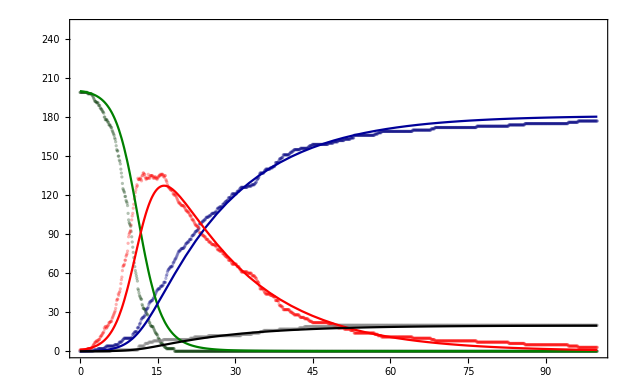

```mathematica
RoughEstimate ={200,0.006,0.0026,0.055};
{𝕤,𝕚,𝕣,𝕕} = SIRDModelSolve[FinalTime,RoughEstimate];

Show[
ListPlot[{FinalNotInfectedList,FinalRecoveredList,FinalInfectedList,FinalDeathsList},PlotRange->{{0,FinalTime},{0,250}},
PlotStyle->{RGBColor[0,0.2,0,0.3],RGBColor[0,0.0,0.5,0.3],RGBColor[0.99,0.0,0.0,0.3],RGBColor[0.5,0.5,0.5,0.3]}],


Plot[{𝕤[t],𝕣[t],𝕚[t],𝕕[t]},{t,0,FinalTime},
PlotStyle->{RGBColor[0,0.5,0],RGBColor[0,0.0,0.6],RGBColor[0.99,0.0,0.0],RGBColor[0.0,0.0,0.0]},Frame->True],Frame->True]
```

{0.00610496,0.00307059,0.0506742}

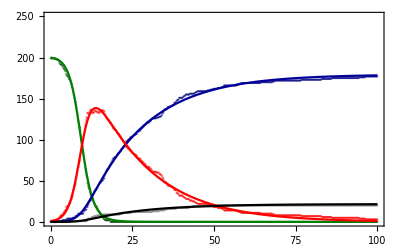

```mathematica
ClearAll[β,γ,α,Chi2,θest,θmin,θmax];
Off[InterpolatingFunction::dmval];
S0=200;
θ={α,β,γ};
n=Length[θ];
θest = {0.006,0.0026,0.055};
θmin = {0.004,0.0016,0.035};
θmax = {0.008,0.0036,0.075};
Qtdeθ={10,10,10};
hθ=MapThread[(#2-#1)/(#3-1)&,{θmin,θmax,Qtdeθ}];
LimDo=MapThread[{#1,#2,#3,#4}&,{θ,θmin,θmax,hθ}];
list={};
count=0;
Monitor[Do[count++;AppendTo[list,Join[{θ},{SIRDModelChiSqrd[FinalTime,Join[{S0},θ]]}]],Evaluate[Sequence@@LimDo]],Row[{"count: ",count}]];


Chi2Kernel=Interpolation[list];
Chi2[θ_]:=Chi2Kernel[Sequence@@θ];


θbf=FindArgMin[ Chi2[θ],Evaluate[Sequence@@MapThread[{#1,#2,#3}&,{θ,θmin,θmax}]]]

{α,β,γ}=θbf;
{𝕤,𝕚,𝕣,𝕕} = SIRDModelSolve[FinalTime,{S0,α,β,γ}];

Show[
ListPlot[{FinalNotInfectedList,FinalRecoveredList,FinalInfectedList,FinalDeathsList},PlotRange->{{0,FinalTime},{0,250}},
PlotStyle->{RGBColor[0,0.2,0,0.3],RGBColor[0,0.0,0.5,0.3],RGBColor[0.99,0.0,0.0,0.3],RGBColor[0.5,0.5,0.5,0.3]}],


Plot[{𝕤[t],𝕣[t],𝕚[t],𝕕[t]},{t,0,FinalTime},
PlotStyle->{RGBColor[0,0.5,0],RGBColor[0,0.0,0.6],RGBColor[0.99,0.0,0.0],RGBColor[0.0,0.0,0.0]},Frame->True],Frame->True]
```